# Unit 2: Differentiation

## Linear approximation

```mathematica
10*0.4+150
```

154.

-Graphics-

```mathematica
D[√x,x]
```

1/(2 √x)

```mathematica
1/(2 √100)
```

1/20

```mathematica
4*%
```

1/5

```mathematica
f[x_]:=x^2.5
f'[4]*-0.03+f[4]
```

31.4

```mathematica
D[√x,{x,2}]
```

-1/(4 x^(3/2))

```mathematica
-1/(4 100^(3/2))
```

-1/4000

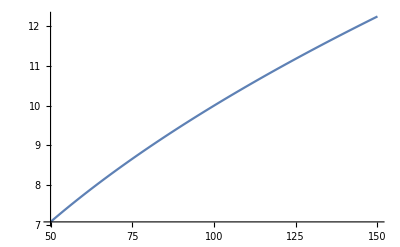

```mathematica
Plot[√x,{x,50,150}]
```

```mathematica
v[x_]:=4π*x^3/3
v'[r]
v'[10]*-0.03
```

4 π r^2

-37.6991

```mathematica
v'[10]
```

400 π

```mathematica
20/400
```

1/20

## Product rule

```mathematica
D[√x,x]*Cos[x]+√x*-Sin[x]
```

Cos[x]/(2 √x)-√x Sin[x]

```mathematica
100*0.4
```

40.

```mathematica
100*-0.01+3*0.4
```

0.2

f(x)=x^2 Sin[x]Cos[x]
f'[x]=2x*Sin[x]*Cos[x]
		 + x^2*-Cos[x] *Sin[x]
	 	+ x^2* Sin[x]*-Sin[x]

## Quotient rule

```mathematica
Limit[(f2*g-f*g2)/t,t->0]
```

Indeterminate

```mathematica
D[(2+Cos[X])/(x^2+1),x]
```

-(2 x (2+Cos[X]))/((1+x^2)^2)

-Graphics-

## Chain rule

-Graphics-

```mathematica
D[120*t+100,t]
```

120

```mathematica
3*0.01+9
```

9.03

```mathematica
4*(9.03-9)+5
```

5.12

```mathematica
Solve[5.12==x*(2.01-2)+5,x]
```

{{x→12.}}

```mathematica
3*4*(5*2)
```

120

#### Examples

```mathematica
f[x_]:=√(x^3+2x+1)
f1[x_]:=1/(2 √(x^3+2x+1))*(3 x^2+2)
f1[1]
```

5/4

```mathematica
g[x_]:=Sin[x^2+2x]
g1[x_]:=-Cos[x^2+2x]*(2x+2)
g1[x]
```

(2+2 x) Cos[2 x+x^2]

#### Exercises

```mathematica
f[x_]:=Sin[x/(x^2+1)]
f1[x_]:= Cos[u]*u'
f2[x_]:= Cos[x/(x^2+1)]*((x^2+1)-(x*2*x))/((x^2+1)^2)
f2[x]==f'[x]
f2[x]
```

True

(-(2 x^2)/((1+x^2)^2)+1/(1+x^2)) Cos[x/(1+x^2)]

```mathematica
k[x_]:=Cos[x]*Sin[x]^4
u:= Sin[x]^4
k1[x_]:= -Sin[x]*u+Cos[x]*u'
inn:= Sin[x]
auss:= x^4
k2[x_]:= -Sin[x]*Sin[x]^4+Cos[x]*(4*(Sin[x])^3*Cos[x])
k'[x] == k2[x]
k2[x]
```

True

4 Cos[x]^2 Sin[x]^3-Sin[x]^5

### Review

```mathematica
g'[f[3]]*f'[3];
g'[5]*3;
4*3

f'[g[3]]*g'(3);
f'[4]*5;
-3*5
```

12

-15

```mathematica
p[i_]:=10*i^2
p'[6]
```

120

## Implicit Differentiation

```mathematica
Solve[x^2+y^2==25,{x,y}]
```

```mathematica
{{y->-√(25-x^2)},{y->√(25-x^2)}}
```

```mathematica
D[√(25-x^2),x]
D[-√(25-x^2),x]
```

-x/(√(25-x^2))

x/(√(25-x^2))

```mathematica
x= -3;
-x/(√(25-x^2))
```

3/4

```mathematica
eclipse := x^4−3 x^2+y^4+y^2+2 x^2 y^2==0
D[2y+Cos[x]+x^2 y+Sin[2y]==3,x]
```

2 x y-Sin[x]==0

```mathematica
y^3+x^3==3xy;
3 y^2*(dy/dx)+3 x^2==3*y+(dy/dx)*x*3;
(3 y^2-3x)*(dy/dx)==3y-3 x^2;
dy/dx==(3y-3 x^2)/(3 y^2-3x);
```

### Practice

```mathematica
y^2==x;
dy/dx==1/(2y)
```

dy/dx==1/(2 y)

```mathematica
x^2+ 4x*y==2 y^2+5;
2x+4y+4x*dy/dx==4y*dy/dx;
2x+4y==(4y-4x)*dy/dx;
(2x+4y)/(4y-4x)==dy/dx
```

(2 x+4 y)/(-4 x+4 y)==dy/dx

```mathematica
u==Sin[y^2+u];
du/dy==Cos[y^2+u]*(2y+du/dy);
du/dy==Cos[y^2+u]*2y+Cos[y^2+u]*du/dy;
(1-Cos[y^2+u])*du/dy==Cos[y^2+u]*2y;
du/dy==(Cos[y^2+u]*2y)/(1-Cos[y^2+u]);
Simplify[(Cos[y^2+u]*2y)/(1-Cos[y^2+u])]
```

-(2 y Cos[u+y^2])/(-1+Cos[u+y^2])

```mathematica
w^2 v^3==w^3 v^2;
2w*dw/dv*v^3+w^2*3 v^2==3 w^2*dw/dv*v^2+w^3*2v;
(2w*v^3-3 w^2*v^2)*dw/dv==w^3*2v-w^2*3 v^2;
dw/dv==Simplify[(w^3*2v-w^2*3 v^2)/(2w*v^3-3 w^2*v^2)]
```

```mathematica
dw/dv==(w (-3 v+2 w))/(v (2 v-3 w))
```

```mathematica
x*y==y^3;
y+dy/dx*x==3 y^2*dy/dx;
(3 y^2-x)*dy/dx==y;
dy/dx==Simplify[y/(3 y^2-x)]
```

dy/dx==-y/(x-3 y^2)

```mathematica
dy/dx==-x/y;
dy/dx==(x*dy/dx-y)/y^2;
dy/dx==x*y^-2*dy/dx-y^-1;
(1-x*y^-2)*dy/dx==-y^-1;
dy/dx==Simplify[-y^-1/(1-x*y^-2)]
```

```mathematica
dy/dx==y/(x-y^2)
```

## Inverse functions

-Graphics-

```mathematica
-2197^(1/3)
```

13 (-1)^(1/3)

```mathematica
Solve[6x-16==4,x]
```

{{x→10/3}}

```mathematica
h[x_]:=3-2/x
h[4]
y==3-2/x;
y-3==-2/x;
1/(y-3)==x/-2;
(1/(y-3))*-2==x;
Simplify[(1/(x-3))*-2]
h1[x_]:=-2/(-3+x)
h1[5/2]
```

5/2

-2/(-3+x)

4

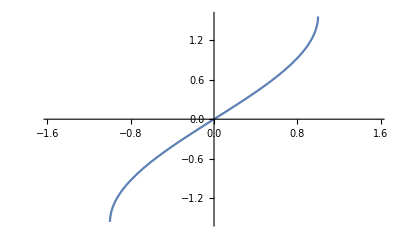

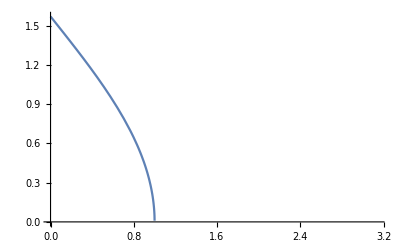

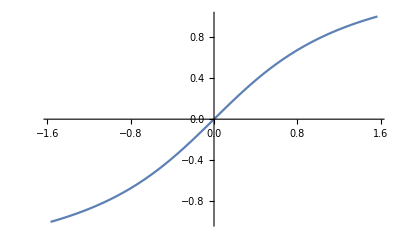

π

-π/2

-π/4

3/5

```mathematica
Plot[ArcSin[x],{x,-π/2,π/2}]
Plot[ArcCos[x],{x,0,π}]
Plot[ArcTan[x],{x,-π/2,π/2}]
ArcCos[-1]
ArcSin[-1]
ArcTan[-1]
Sin[ArcTan[3/4]]
```

```mathematica
y==5/2 x-3;
Solve[y==5/2 x-3,x]
```

{{x→(2 (3+y))/5}}

```mathematica
h'[2]==1/g'[h[2]];
h'[2]==1/g'[3/2];
h'[2]==1/4
```

h'[2]==1/4

```mathematica
f[x_]:= -2 x^3-7x+5;
g[x_]:=InverseFunction[f][x]
g[5]
g'[5]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

0

-1/7

-1/280

```mathematica
D[ArcTan[x],x]
```

1/(1+x^2)

```mathematica
InverseFunction[ArcTan[3#]&][x]
```

ConditionalExpression[Tan[x]/3, ]

```mathematica
D[ArcTan[3*#] ,#]/.#->-1
```

3/10

```mathematica
D[#^2*ArcCos[#],#]/.#->1/2
```

-1/(2 √3)+π/3

```mathematica
Re[N[ArcSin[2]+ArcCos[2]]]
```

1.5708

## Exponential functions

-Graphics-

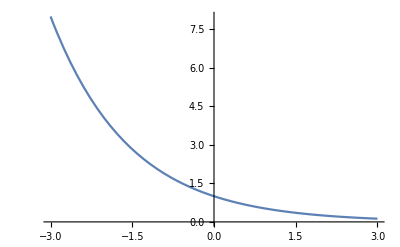

```mathematica
Plot[(1/2)^x,{x,-3,3}]
```

-Graphics-

```mathematica
e^4.5*0.05-e^4.5;
90*0.05+90
```

94.5

```mathematica
0.5a(ⅇ^(x/a)+ⅇ^(-x/a))/.a->2
Simplify[D[%,x]]
```

1. (ⅇ^(-x/2)+ⅇ^(x/2))

-Graphics-

## Logarithms

-Graphics-

```mathematica
Log[10,1000]
Log[10,0.000001]
```

3

-6.

```mathematica
Log[2]
```

Log[2]

```mathematica
N[Log[20]]
```

2.99573